```mathematica
(* Note, unless specified all these have to be considered equations, i.e. ==0 *)
```

```mathematica
(* Linear matter evolution in an Einstein de Sitter universe *)
diff=δ''[a]+3/(2 a) δ'[a]-3/(2 a^2) δ[a]
```

-(3 δ[a])/(2 a^2)+(3 δ'[a])/(2 a)+δ''[a]

```mathematica
(* The general solution to this is (g is the growing mode coefficient and d is the decaying mode one) *)
sol=δ[a]->g a+d a^(-3/2)
dsol=D[sol,a]
ddsol=D[dsol,a]
```

δ[a]→d/a^(3/2)+a g

δ'[a]→-(3 d)/(2 a^(5/2))+g

δ''[a]→(15 d)/(4 a^(7/2))

```mathematica
(* Let's prove it *)
diff;
% //.ddsol // Expand;
% //.dsol // Expand;
% //.sol // Expand
```

0

```mathematica
(* Let's now solve the differential equation in different cases, always between amin==10^(-10) to amax==1 *)
amin=10.^(-3)
amax=1.
```

0.001

1.

```mathematica
(* These are the initial conditions for δ and it's derivative, expressed as a function of aini (which can be either the start or the end) *)
rδ=δ[a] //.sol //.a->aini;
rδp=δ'[a] //.dsol //.a->aini;
```

```mathematica
(* only growing mode starting from minimum a *)
pars={aini->amin,aend->amax,g->1,d->0}
solgmin=Flatten@NDSolve[{diff==0,δ[aini]==rδ,δ'[aini]==rδp} //.pars,δ[a],{a,aini,aend} //.pars]
```

{aini→0.001,aend→1.,g→1,d→0}

{δ[a]→InterpolatingFunction[…][a]}

```mathematica
(* only decaying mode starting from minimum a *)
pars={aini->amin,aend->amax,g->0,d->1}
soldmin=Flatten@NDSolve[{diff==0,δ[aini]==rδ,δ'[aini]==rδp} //.pars,δ[a],{a,aini,aend} //.pars]
```

{aini→0.001,aend→1.,g→0,d→1}

{δ[a]→InterpolatingFunction[…][a]}

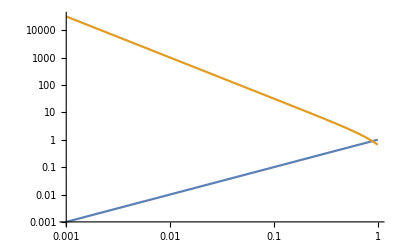

```mathematica
LogLogPlot[{δ[a] //.solgmin,δ[a] //.soldmin},{a,amin,amax}]
```

## Loglog

```mathematica
(* Note, unless specified all these have to be considered equations, i.e. ==0 *)
```

```mathematica
(* Note also that to stabilise the solution we use n==ln(a) as our time variable *)
```

```mathematica
(* Linear matter evolution in an Einstein de Sitter universe *)
diff=δ''[n]+1/2 δ'[n]-3/2 δ[n]
```

-(3 δ[n])/2+δ'[n]/2+δ''[n]

```mathematica
(* The general solution to this is (g is the growing mode coefficient and d is the decaying mode one) *)
sol=δ[n]->g Exp[n]+d Exp[-3 n/2]
dsol=D[sol,n]
ddsol=D[dsol,n]
```

δ[n]→d ⅇ^(-3 n/2)+ⅇ^n g

δ'[n]→-3/2 d ⅇ^(-3 n/2)+ⅇ^n g

δ''[n]→9/4 d ⅇ^(-3 n/2)+ⅇ^n g

```mathematica
(* Let's prove it *)
diff;
% //.ddsol // Expand;
% //.dsol // Expand;
% //.sol // Expand
```

0

```mathematica
(* Let's now solve the differential equation in different cases. Here we fix the minimum and maximum values *)
nmin=-10
nmax=0.
```

-10

0.

```mathematica
(* These are the initial conditions for δ and it's derivative, expressed as a function of nini (which can be either the start or the end) *)
rδ=δ[n] //.sol //.n->nini
rδp=δ'[n] //.dsol //.n->nini
```

d ⅇ^(-3 nini/2)+ⅇ^nini g

-3/2 d ⅇ^(-3 nini/2)+ⅇ^nini g

{nini→-10,nend→0.,g→1,d→0}

{δ[n]→InterpolatingFunction[…][n]}

{nini→-10,nend→0.,g→0,d→1}

{δ[n]→InterpolatingFunction[…][n]}

{nini→0.,nend→-10,g→1,d→0}

{δ[n]→InterpolatingFunction[…][n]}

{nini→0.,nend→-10,g→0,d→1}

{δ[n]→InterpolatingFunction[…][n]}

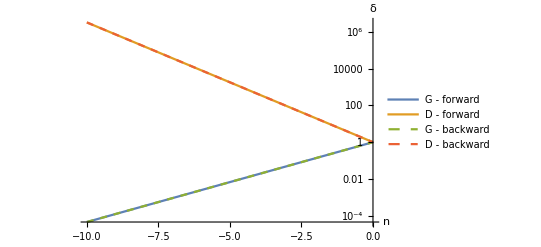

```mathematica
(* only growing mode starting from minimum n *)
pars={nini->nmin,nend->nmax,g->1,d->0}
solgmin=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
(* only decaying mode starting from minimum n *)
pars={nini->nmin,nend->nmax,g->0,d->1}
soldmin=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
(* only growing mode starting from maximum n *)
pars={nini->nmax,nend->nmin,g->1,d->0}
solgmax=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
(* only decaying mode starting from maximum n *)
pars={nini->nmax,nend->nmin,g->0,d->1}
soldmax=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
LogPlot[{δ[n] //.solgmin,δ[n] //.soldmin,δ[n] //.solgmax,δ[n] //.soldmax},{n,nmin,nmax},PlotLegends->{"G - forward", "D - forward","G - backward","D - backward"},AxesLabel->{"n","δ"},PlotStyle->{Automatic,Automatic,Dashed,Dashed}]
```

```mathematica
(* In the plot above everything is as expected, having the growing/decaying solution both forward and backward in time gives the same result *)
```

```mathematica
(* Now we can do the same excercise but with a small epsilon contaminating the wanted solution *)
epsilon=10.^-6
```

1.×10^-6

{nini→-10,nend→0.,g→1,d→0}

{δ[n]→InterpolatingFunction[…][n]}

{nini→-10,nend→0.,g→1.×10^-6,d→1}

{δ[n]→InterpolatingFunction[…][n]}

{nini→0.,nend→-10,g→1,d→1.×10^-6}

{δ[n]→InterpolatingFunction[…][n]}

{nini→0.,nend→-10,g→0,d→1}

{δ[n]→InterpolatingFunction[…][n]}

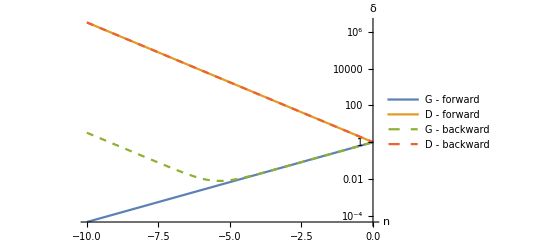

```mathematica
(* only growing mode starting from minimum n *)
pars={nini->nmin,nend->nmax,g->1,d->0}
solgmin=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
(* only decaying mode starting from minimum n *)
pars={nini->nmin,nend->nmax,g->epsilon,d->1}
soldmin=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
(* only growing mode starting from maximum n *)
pars={nini->nmax,nend->nmin,g->1,d->epsilon}
solgmax=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
(* only decaying mode starting from maximum n *)
pars={nini->nmax,nend->nmin,g->0,d->1}
soldmax=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
LogPlot[{δ[n] //.solgmin,δ[n] //.soldmin,δ[n] //.solgmax,δ[n] //.soldmax},{n,nmin,nmax},PlotLegends->{"G - forward", "D - forward","G - backward","D - backward"},AxesLabel->{"n","δ"},PlotStyle->{Automatic,Automatic,Dashed,Dashed}]
```

```mathematica
`
```

```mathematica
(* In this plot we can see that if we evolve back in time a mode that have a growing mode and a little contamination from the decaying one, we end up following the decaying solution at early times (which is the growing one back in time) *)
```

```mathematica
(* Now we solve as in the same plot but anticipating initial time *)
(* Let's now solve the differential equation in different cases. Here we fix the minimum and maximum values *)
nmin=-20
```

-20

{nini→-20,nend→0.,g→1,d→0}

{δ[n]→InterpolatingFunction[…][n]}

{nini→-20,nend→0.,g→0,d→1}

{δ[n]→InterpolatingFunction[…][n]}

{nini→0.,nend→-20,g→1,d→0}

{δ[n]→InterpolatingFunction[…][n]}

{nini→0.,nend→-20,g→0,d→1}

{δ[n]→InterpolatingFunction[…][n]}

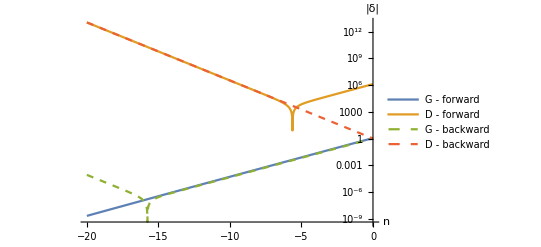

```mathematica
(* only growing mode starting from minimum n *)
pars={nini->nmin,nend->nmax,g->1,d->0}
solgmin=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
(* only decaying mode starting from minimum n *)
pars={nini->nmin,nend->nmax,g->0,d->1}
soldmin=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
(* only growing mode starting from maximum n *)
pars={nini->nmax,nend->nmin,g->1,d->0}
solgmax=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
(* only decaying mode starting from maximum n *)
pars={nini->nmax,nend->nmin,g->0,d->1}
soldmax=Flatten@NDSolve[{diff==0,δ[nini]==rδ,δ'[nini]==rδp} //.pars,δ[n],{n,nini,nend} //.pars]
LogPlot[{Abs[δ[n] //.solgmin],Abs[δ[n] //.soldmin],Abs[δ[n] //.solgmax],Abs[δ[n] //.soldmax]},{n,nmin,nmax},PlotLegends->{"G - forward", "D - forward","G - backward","D - backward"},AxesLabel->{"n","|δ|"},PlotStyle->{Automatic,Automatic,Dashed,Dashed}]
```

```mathematica
(* Here we are plotting the absolute value of δ. You can see that there is a sign change in δ for a couple of curves. In particular, they are the curves that decrease in the time variable (the decaying mode with forward evolution, and the growing mode with backward evolution). This is because, as they approach zero, these curves cross it by numerical error. After crossing it they start following the corresponding growing mode. *)
```